## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[4];
```

## Utility Functions

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a,b,h}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a-m*h,b,h}]//N;

Return[xs];
]
```

```mathematica
kGrid[p_]:=Module[{kmin,kmax,numk,kh},
kmin=p["kmin"];
kmax=p["kmax"];
numk = p["numk"];
kh = (kmax-kmin)/(numk-1);

Return[Table[k,{k,kmin,kmax,kh}]];
];
```

```mathematica
yvec[k_,p_]:=Module[{n,m, h,cDiffCoeffs,numNonzero, nonZeroElements},
n=p["n"];
m=p["m"];
h = p["h"];

cDiffCoeffs={1,-2,1};

nonZeroElements={
n+m->-cDiffCoeffs[[1]],
n+m+1->-1*(
cDiffCoeffs[[1]]*Exp[Sqrt[2]*I*k*h]+
cDiffCoeffs[[2]]+2*h^2*k^2)
};

Return[SparseArray[nonZeroElements,{n+m+1}]];
]
```

```mathematica
yvecKVec[kVec_,p_]:=Table[yvec[k,p],{k,kVec}]
```

```mathematica
D2Matrix[p_]:= Module[{n,m,cDiffCoeffs,bands},
n=p["n"];
m=p["m"];

cDiffCoeffs={1,-2,1};

bands=Table[Band[{1,i}]->cDiffCoeffs[[i]],{i,1,Length[cDiffCoeffs]}];

Return[SparseArray[bands,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrix[k_,p_]:=Module[{ n,m, h, band},
n=p["n"];
m=p["m"];
h = p["h"];

(*band = Band[{1,3}]->2*h^2*k^2;*)
band = Band[{1,2}]->2*h^2*k^2;
Return[SparseArray[band,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrixKVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,Vparams_,SEDict_]:=Module[{xg,n,m, h, u1V, matV},
xg=xgrid[SEDict][[2;;-1]];
n=SEDict["n"];
m=SEDict["m"];
h =SEDict["h"];

u1V=Band[{m+1,m+2}]->2*h^2*V[xg,Vparams];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[matV];
];
```

## Solve Schrodinger equation and calculate cost

```mathematica
SchrEqOfV[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=Module[{VV, soln},
VV = VMatrix[V,VParams, SEDict];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]],Method->"Banded"]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
TofV[k_,x1_,x2_,SEsol1_,SEsol2_]:=Module[{},
Exp[I*Sqrt[2]*k*x2]*(1-Exp[-I*2*Sqrt[2]*k*(x2-x1)])/
(SEsol2-SEsol1*Exp[-I*Sqrt[2]*k*(x2-x1)])
];
```

```mathematica
TofVVec[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=
Module[{step,solk,xgf,x1,x2,Tk},
step=SEDict["TCalcStep"];
solk=SchrEqOfV[V,VParams,SEDict,kVec,D2,EMatrixVector,yVector];
xgf=xgridFull[SEDict];
x1=xgf[[1]];
x2=xgf[[step]];

Tk=Table[{
sol[[1]], 
TofV[sol[[1]],x1,x2, sol[[2,1]],sol[[2,step]]]
},
{sol,solk}];

Return[Tk];
]
```

```mathematica
Cost[T_, TGoal_, weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{Tdiff, cost},
(*Calculate difference in vectors*)
Tdiff=Table[{T[[i,1]],Abs[T[[i,2]]-TGoal[[i,2]]]^2},{i,1,Length[T]}];

(*Calculate loss. Estimate integral using midpoint rule. Normalize by interval. *)
cost = Sum[(Tdiff[[i+1,1]]-Tdiff[[i,1]]) * 1/2 * (weights[[i]]*Tdiff[[i,2]]+weights[[i+1]]*Tdiff[[i+1,2]]),{i,1,Length[T]-1}] / Sum[(Tdiff[[i+1,1]]-Tdiff[[i,1]]) * 1/2 * (weights[[i]]+weights[[i+1]]),{i,1,Length[T]-1}];
Return[cost];
];
```

## Search for the potential

```mathematica
BackgroundWeights[k_]:=Sqrt[Sinh[Pi Sqrt[2]k]^2/(Sinh[Pi Sqrt[2]k]^2+Cosh[Pi Sqrt[7]/2]^2)]
```

```mathematica
CustomStepMonitor[TGoal_,Vfunc_,Vpars_,SEDict_,kVec_ ,d2_,eMatrix_,yvec_,weights_:Table[1,{i,1,Length[TGoal_]}]]:=
Module[{tvec,cost,PlotA,PlotB},
tvec=TofVVec[Vfunc, Vpars,SEDict,kVec,d2,eMatrix,yvec];
cost=Cost[Abs[tvec], TGoal, weights];

(*ALERT: very bad programming!!!*)
If[cost≠lastCost,
Print["Cost: ", cost];
Print["Params: ",Vpars]; 

PlotA=Plot[Vfunc[x,Vpars],{x,SEDict["a"],SEDict["b"]},PlotRange->All];
PlotB=ListPlot[{TGoal,Abs[tvec]},PlotRange->All,PlotLabel->"Cost: "<>ToString[cost]];

Print[GraphicsRow[{PlotA,PlotB}, ImageSize->Large]]
];

lastCost=cost;
(*Print both plots. Magic from mathematica stackexchange: https://mathematica.stackexchange.com/questions/80224/use-a-module-to-return-multiple-plots*)
(*CellPrint@ExpressionCell[#,"Output"]&/@{PlotA,PlotB};*)
]
```

```mathematica
SearchPotential [
TGoal_,Vfunc_,Vpars_,parConstrs_,SEDict_,kVec_, 
weights_:Table[1,{i,1,Length[TGoal_]}],
method_:{
"DifferentialEvolution", 
"Tolerance"->0.1,
"PostProcess"->False, 
"ScalingFactor"->0.75,
 "CrossProbability"->0.5}
]:=
Module[{VparsFlat, soln,d2mat,emat,yyvec,lastCost},
VparsFlat=Flatten[Vpars];
d2mat = D2Matrix[SEDict];
emat=EMatrixKVec[kVec,SEDict];
yyvec=yvecKVec[kVec,SEDict];

lastCost=1000;

soln=NMinimize[{
Hold[Cost[Abs[TofVVec[Vfunc, Vpars,SEDict,kVec,d2mat,emat,yyvec]], TGoal,weights]],
parConstrs
},
VparsFlat, 
Method->method, 
AccuracyGoal->2,
PrecisionGoal->2,
MaxIterations->500,
StepMonitor:> Hold[Catch[CustomStepMonitor[TGoal, Vfunc,Vpars,SEDict,kVec,d2mat,emat,yyvec,weights]]]
];

Return[soln];
]
```

## Define actual search parameters and potentials

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_]:=Module[{pot},
pot=Sum[VGauss[x,pars],{pars,params}];
Return[pot];
];
```

```mathematica
SEDict = Association["a"->-10, "b"->10,"n"->500,"m"->100,"kmin"->0.01,"kmax"->2.001,"numk"->100, "TCalcStep"->25];
SEDict["h"]=(SEDict["b"]-SEDict["a"])/SEDict["n"];
kgrid = kGrid[SEDict];
```

## “Low pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[0.5-k]},{k,kgrid}];
```

```mathematica
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

```mathematica
(*SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kgrid,
weightsofKGoalCool]*)
```

## “High-pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[k-0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

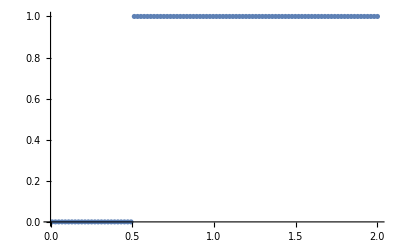

```mathematica
ListPlot[TofKGoalCool]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kVecTest]*)
```

## “Low-pass quantum filter” 3 gaussians

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[-k+0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

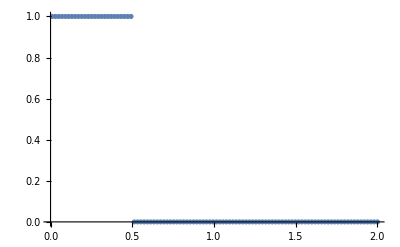

```mathematica
ListPlot[{TofKGoalCool}]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}},
{sigma1>0.01,sigma2>0.01,sigma3>0.01,x01+x02+x03==0},
SEDict,
kVecTest,
weightsofKGoalCool]*)
```

## “k=1 comb” 4 gaussians

```mathematica
TofKGoalCool=Table[{k,
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]},{k,kgrid}];
weightsofKGoalCool=Log[1+Table[(1+(Length[kgrid]-1)*(
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]))+
BackgroundWeights[k],{k,kgrid}]]^2;
```

```mathematica
1.25/2
```

0.625

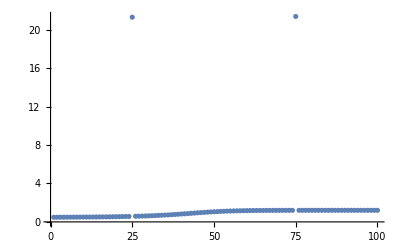

```mathematica
ListPlot[weightsofKGoalCool,PlotRange->All]
```

Cost: 0.41192

Params: {{0.961866,-0.849004,0.383273},{0.863603,0.166569,1.91307},{0.976933,0.507811,0.858854},{-0.0786527,0.174625,0.784734}}

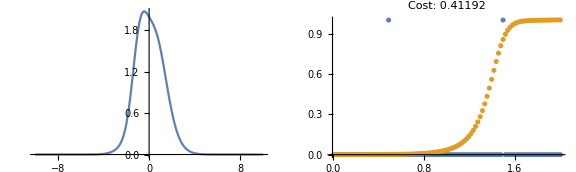

Cost: 0.321556

Params: {{0.358296,-0.00709719,0.418647},{2.81988,-0.141908,1.34999},{0.519667,-0.237134,2.95283},{1.52072,0.386139,0.469093}}

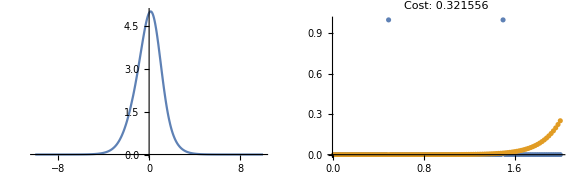

Cost: 0.313219

Params: {{0.862514,-0.340691,1.2125},{3.02559,-0.518181,0.126957},{-0.193654,0.576829,0.534949},{1.3807,0.282042,2.04376}}

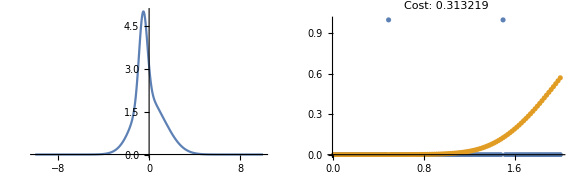

Cost: 0.30486

Params: {{1.5864,-0.477025,0.0500331},{3.09034,-0.457205,0.0910579},{-0.535918,0.305593,1.49213},{0.679591,0.628637,2.61238}}

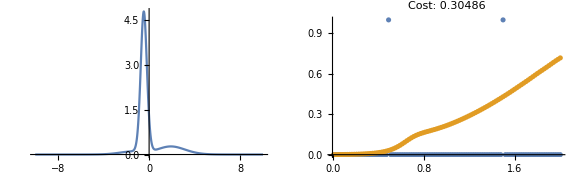

Cost: 0.258565

Params: {{2.82243,0.0776074,0.643373},{2.9773,-2.0383,0.157339},{0.148511,0.689485,1.81081},{0.2274,1.27121,0.851245}}

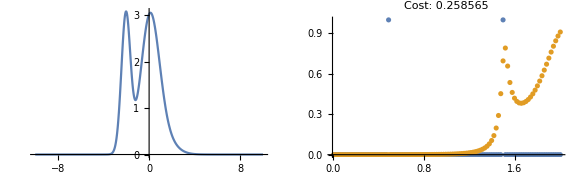

Cost: 0.256165

Params: {{5.20433,1.72596,0.0935648},{-0.262407,1.05134,2.64204},{1.87496,-1.48945,0.917256},{0.393588,-1.28785,0.0774506}}

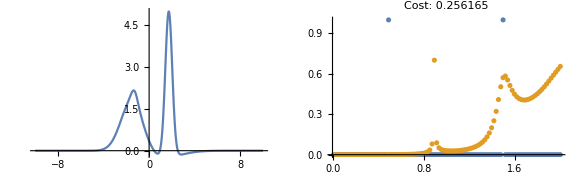

Cost: 0.251085

Params: {{-1.72257,1.72596,0.0935648},{10.9923,1.05134,0.0122548},{-1.23579,-1.48945,0.917256},{0.393588,-1.28785,0.49395}}

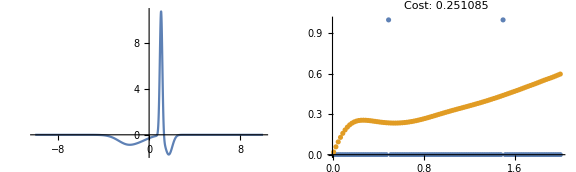

Cost: 0.245835

Params: {{-2.34581,-1.19395,4.43204},{14.8624,-2.18724,0.0108611},{-2.9476,1.49796,0.404853},{0.93433,1.88323,0.870641}}

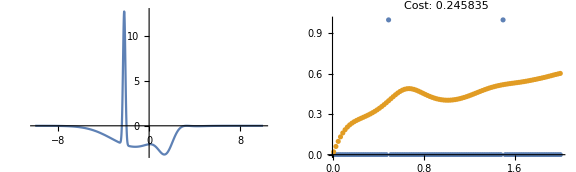

Cost: 0.227967

Params: {{-2.09517,-9.39088,4.40761},{17.0202,-0.586975,0.0101498},{-2.42476,8.60088,0.0125334},{-0.109626,1.37697,0.0379011}}

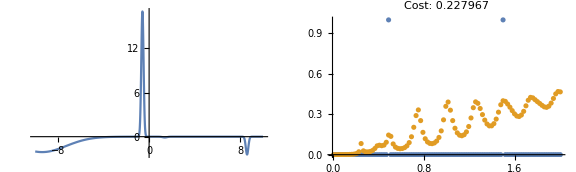

Cost: 0.226265

Params: {{-1.12144,-1.26756,4.41391},{22.4803,-2.41127,0.0100716},{-3.52399,1.54869,0.0214809},{-1.5923,2.13014,0.426155}}

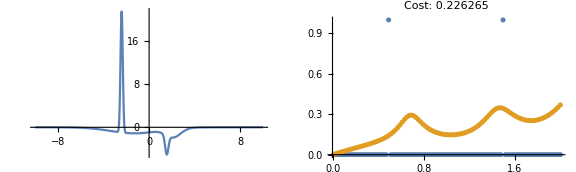

Cost: 0.211024

Params: {{-1.52293,-16.7645,1.66878},{17.5955,3.02616,0.0100698},{-0.93714,10.3113,1.47478},{-1.25226,3.4271,1.16904}}

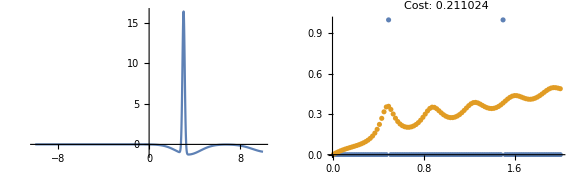

Cost: 0.209587

Params: {{-2.13674,-9.05681,0.0100074},{19.8766,2.20314,0.0100548},{1.59392,5.29328,0.0100096},{-2.43545,1.56039,0.41569}}

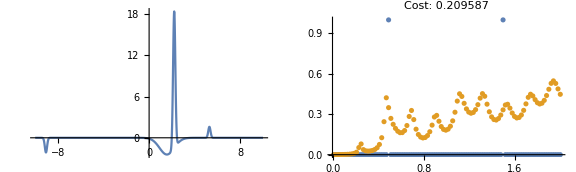

Cost: 0.207682

Params: {{-0.665502,-9.84163,1.72585},{14.8748,-3.75054,0.0100585},{-11.5276,12.8173,0.0100093},{-7.00762,0.774919,0.0100018}}

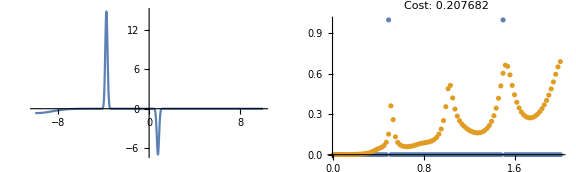

Cost: 0.204282

Params: {{0.171472,-1.12525,0.905166},{25.1485,3.20475,0.0100658},{-2.52601,-0.56564,0.0100405},{3.24401,-1.51386,2.80788}}

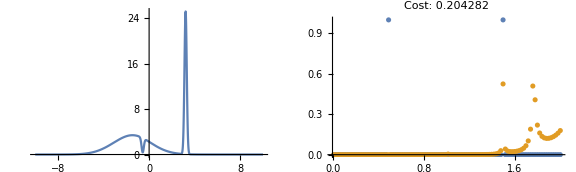

Cost: 0.204184

Params: {{-1.55068,4.2805,1.24192},{12.4583,5.33557,0.0100001},{-5.13701,-9.64349,3.40835},{-2.012,0.0274128,1.47587}}

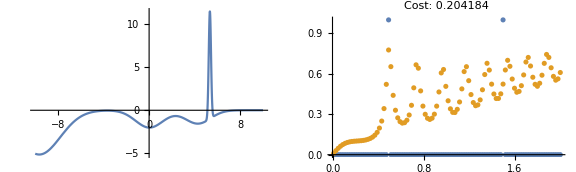

Cost: 0.172872

Params: {{-6.19931,-4.37584,11.1118},{22.4803,0.697009,0.0100946},{-3.52399,1.54869,0.693506},{5.81568,2.13014,0.426155}}

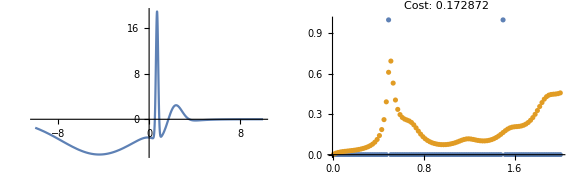

Cost: 0.165377

Params: {{-1.27215,-8.54985,8.79122},{14.4107,-5.44921,0.01},{-12.3362,12.1085,0.01},{-5.45904,1.89055,0.01}}

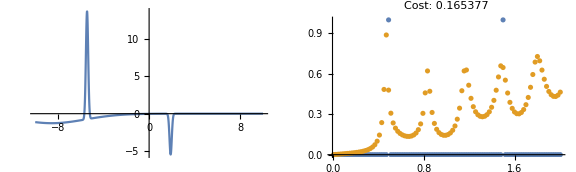

Cost: 0.138667

Params: {{-11.3897,-0.954337,15.4173},{23.0592,-5.8202,0.0100173},{-15.8271,6.78952,0.01},{-12.1221,-0.0149749,0.0397965}}

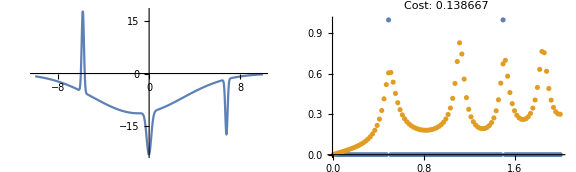

Cost: 0.131181

Params: {{-9.66397,9.64397,4.12631},{14.8748,-3.75054,0.0100585},{-13.018,-6.66835,1.46975},{-9.81123,0.774919,0.0100018}}

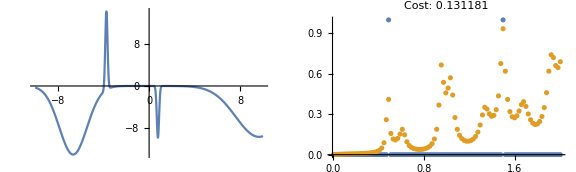

Cost: 0.119232

Params: {{-7.58163,-20.1183,0.632306},{15.0481,-4.41577,0.01},{-9.51964,24.354,0.01},{-13.2527,0.180131,0.01}}

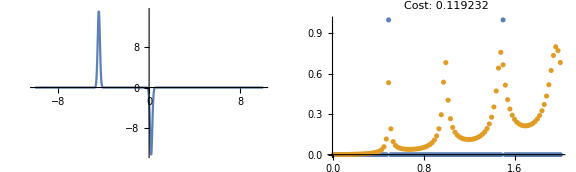

Cost: 0.11833

Params: {{-3.95773,-20.1183,10.0015},{15.0481,-4.41577,0.01},{25.878,24.354,0.01},{-13.2527,0.180131,0.01}}

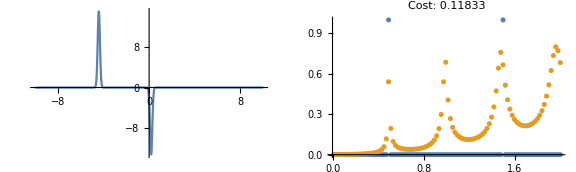

Cost: 0.0998084

Params: {{-13.7856,1.45946,11.4152},{20.3827,-4.58707,0.0101004},{26.3133,1.41282,0.01},{-4.84107,1.71479,0.01}}

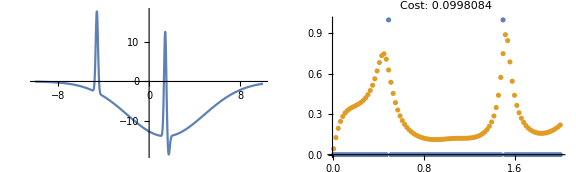

{0.0998084,{A1→-13.7856,x01→1.45946,sigma1→11.4152,A2→20.3827,x02→-4.58707,sigma2→0.0101004,A3→26.3133,x03→1.41282,sigma3→0.01,A4→-4.84107,x04→1.71479,sigma4→0.01}}

```mathematica
solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3},
{A4,x04,sigma4}},
{sigma1>0.01,
sigma2>0.01, 
sigma3>0.01,
sigma4>0.01,
x01+x02+x03+x04==0},
SEDict,
kgrid,
weightsofKGoalCool]
```